# Billiards in a Cusp

## Function Definitions

```mathematica
GetUnitTangent[f_, dom_, pt_] :=Normalize[N[Flatten[D[f,t]/.NSolve[f[[1]] == pt[[1]] && t ∈ dom ,t]]]];
```

```mathematica
(* Reflect vector v over the UNIT VECTOR u *)
ReflectVec[v_, u_] := 2(Dot[v,u])u - v;
```

```mathematica
(* finds intersection of curve param. by f and the RAY generated by v *)
(* f is required to be parametrized by t *)
FindIntersection[f_, dom_, v_, pt_] := Flatten[
(pt + v s)/.If[
Length[#]==0,
{s->10},
#]&@
Flatten[MinimalBy[ 
NSolve[
pt[[1]] + v[[1]] s == f[[1]] && pt[[2]] + v[[2]] s == f[[2]] && s>=0 && t ∈ dom, 
{t, s}
],
t/.# &]
]
];
```

```mathematica
NextPt[pt_,v_] := ({#, ReflectVec[v,GetUnitTangent[c,Interval[{cdom[[2]],cdom[[3]]}], #]]}&@FindIntersection[c, Interval[{cdom[[2]], cdom[[3]]}], v, pt]);
```

## Unit Tests

These only need to be run if you change function definitions above.

### Unit Tangents

```mathematica
cases = {

{ 
{Cos[t], Sin[t]},
Interval[{0,2Pi}],
Table[
{ 
{Cos[t], Sin[t]},
{-Sin[t],Cos[t]} 
},
{t, 0, 2Pi, 2Pi/10}
]
},

{
{t-Sin[t], 1-Cos[t]},
Interval[{0, 2Pi}],
Table[
{ 
{t-Sin[t], 1-Cos[t]},
{1-Cos[t], Sin[t]} 
},
{t, 0, 2Pi, 2Pi/10}
]
}

};

res[case_] := Map[
GetUnitTangent[case[[1]],case[[2]],First[#] ]  == Last[#]&, case[[3]]
];

Map[If[ And@@res[#],Print["Pass"],Print["Fail"]] &, cases];
```

Fail

Fail

### Find Intersection

```mathematica
cases = {

{ 
{t, 3},
Reals,
{1,2},
{0,0},
{3/2,3}
},

{
{Cos[t], Sin[t]},
Interval[{0,2Pi}],
{0,1},
{1/2,0},
{Cos[Pi/3],Sin[Pi/3]}
}

};

res[case_] := FindIntersection[case[[1]],case[[2]], case[[3]] , case[[4]]] == case[[5]];
Map[If[ res[#],Print["Pass"],Print["Fail"]] &, cases];
```

Pass

Pass

## Simulation

### Define Two Curves and Initial Conditions

```mathematica
f = (1/2){Cos[t], Sin[t]}+{0,3/2};
fdom ={t, Pi/2,Pi};
```

```mathematica
g = 2{Cos[t], Sin[t]};
gdom = {t, Pi/2,Pi};
```

```mathematica
initpt = f/.{t->5Pi/8};
initv = {.2,1};
n=6;
```

### Run Simulation

```mathematica
pts = { {initpt, initv} };
Dynamic[i]
c = g;
cdom = gdom;
For[ i = 1, i <n, i = i +1, 
AppendTo[pts, NextPt@@Last[pts]]; 
If[ 
TrueQ[c == g], 
(c = f; cdom = fdom),
(c = g; cdom=gdom)
]
]
```

### Generate Plots

```mathematica
bg = Show[
{
Apply[ParametricPlot[#1,  #2, PlotRange->Full] & , {f, fdom}], 
Apply[ParametricPlot[#1,  #2] & ,{g, gdom}]
},
PlotRange->{ {-1/4,0}, {1.5,2}}
];
ϵ = .05;
eplg = Map[ #[[1]] &, pts];
Join[ 
{Red, Thick, Line[eplg]}, 
Table[ 
If[
EvenQ[n],
{Green,Thin,Line[{{ 0, 0}, eplg[[n]]}], Line[{eplg[[n]], (1+ϵ) eplg[[n]]}]},
{Magenta,Thin,Line[{ { 0, 3/2}, eplg[[n]]}], Line[{eplg[[n]], eplg[[n]] + 2 ϵ(eplg[[n]]-{ 0, 3/2})}]}
],
{n, 1, Length[eplg]}
]
];
plt = Show[bg, Graphics[%]];
```

### Plots

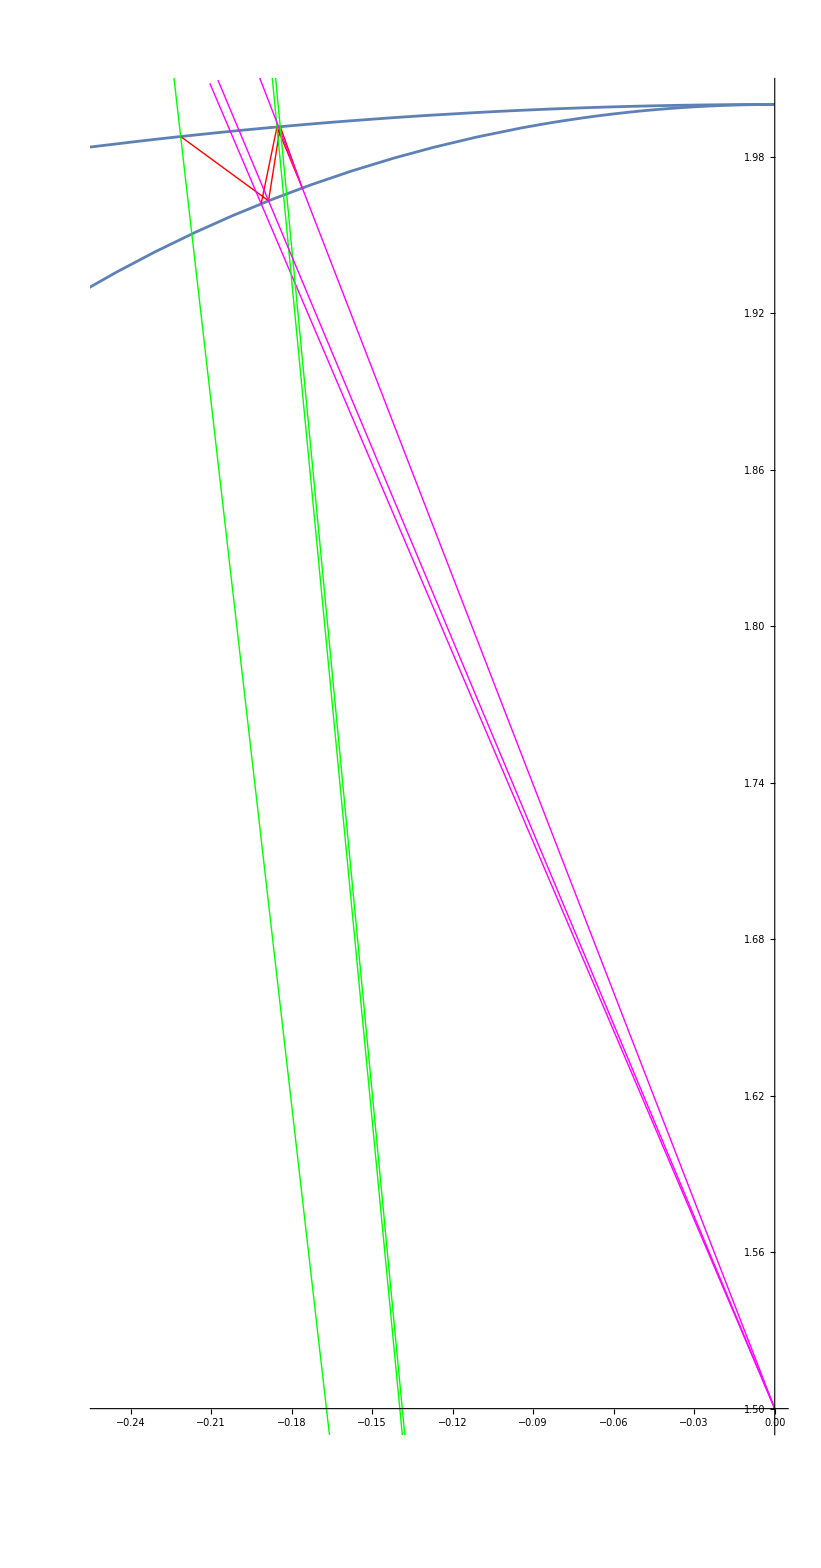

```mathematica
plt
```